## A Minimal Model for Computer Security

```mathematica
RuleSequencePlot[{n_, k_, r_}, ops:OptionsPattern[{ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
ArrayPlot[{IntegerDigits[n, k, k^(2r+1)]},ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize], ops]
```

```mathematica
Epilog->
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{{837471554865,3,1}, {837428508144, 3, 1}})}]["ExplicitPositions"][[1]]},
Arrow[{{loc, 1}, {loc, 0}}]]
```

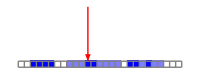

```mathematica
Show[RuleSequencePlot[{837428508144, 3, 1},ColorRules->Automatic, Mesh->True, ColorFunction->(Blend[{White, Blue}, #]&), ImageSize->{200, Automatic}],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{{837471554865,3,1}, {837428508144, 3, 1}})}]["ExplicitPositions"][[1, 2]] +.5},
Graphics[{Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
]
```

```mathematica
Module[{rule ={837428508144, 3, 1},sp,cf, is, murule = {837471554865,3,1}},
cf = (Blend[{White, Blue}, #]&);
is = {200, Automatic};
 sp = RuleSequencePlot[rule,ColorRules->Automatic, ColorFunction->cf, ImageSize->is]; 
GraphicsRow[GraphicsColumn/@
{{sp, ArrayPlot[CellularAutomaton[rule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorFunction->cf, ImageSize->is, Mesh->True, MeshStyle->Opacity[.2], Frame->True]},
{Show[RuleSequencePlot[murule,ColorRules->Automatic, ColorFunction->cf, ImageSize->is],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{murule, rule})}]["ExplicitPositions"][[1, 2]] -.5},
Graphics[{Style[Text["Compromise", {loc, 12}], Italic],Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
, ImageSize->is],
ArrayPlot[CellularAutomaton[murule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorFunction->cf, ImageSize->is, Mesh->True, MeshStyle->Opacity[.2]]}
}, Alignment->Bottom]]
```

-Graphics-

```mathematica
Module[{rule ={837428508144, 3, 1},sp,cf, is, murule = {837471554865,3,1}},
is = {200, Automatic};
 sp = RuleSequencePlot[rule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is]; 
GraphicsRow[GraphicsColumn/@
{{sp, ArrayPlot[CellularAutomaton[rule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]},
{Show[RuleSequencePlot[murule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{murule, rule})}]["ExplicitPositions"][[1, 2]] -.5},
Graphics[{Style[Text["Compromise", {loc, 12}], Italic],Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
, ImageSize->is],
ArrayPlot[CellularAutomaton[murule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]}
}, Alignment->Bottom]]
```

-Graphics-

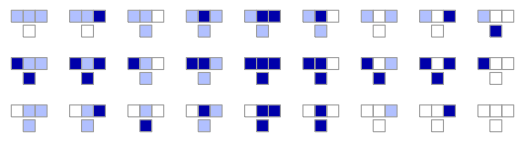

```mathematica
RulePlot[CellularAutomaton[{837428508144, 3, 1}],ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}]
```

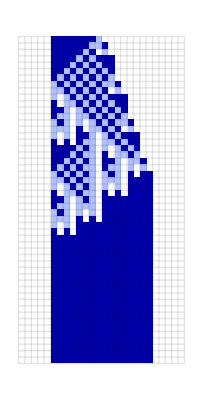

```mathematica
ArrayPlot[CellularAutomaton[{837428508144, 3, 1},{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, Mesh->True, MeshStyle->Opacity[.1]]
```

```mathematica
Module[{rule ={837428508144, 3, 1},sp,cf, is, murule = {837471554865,3,1}},
is = {200, Automatic};
 sp = RulePlot[rule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is]; 
GraphicsRow[GraphicsColumn/@
{{sp, ArrayPlot[CellularAutomaton[rule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.2], Frame->True]},
{Show[RuleSequencePlot[murule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{murule, rule})}]["ExplicitPositions"][[1, 2]] -.5},
Graphics[{Style[Text["Compromise", {loc, 12}], Italic],Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
, ImageSize->is],
ArrayPlot[CellularAutomaton[murule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.2]]}
}, Alignment->Bottom]]
```